```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
Simplify[verts]
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,Simplify[{2d,0,z}],Simplify[{Norm[z]^2/r-r,1/r,z/r}]];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[RootApproximant[Vnye]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.0001],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.0001](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

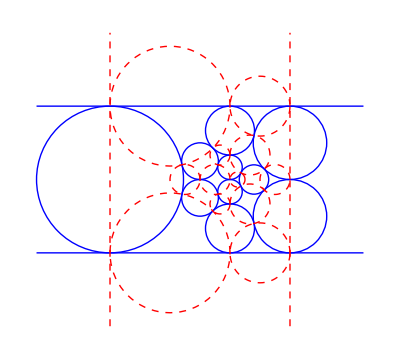
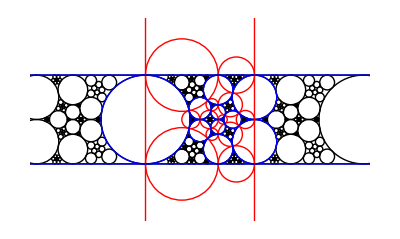
-Graphics-
-Graphics-
(144 | 1 | 4 √6 | 7
72 | 2/3 | 2 √6 | 5
48 | 2/3 | 2 √6 | 3
120 | 1 | 4 √6 | 5
144 | 5/6 | 4 √6 | 5
96 | 1/2 | 2 √6 | 5
0 | 1/6 | 0 | 1
48 | 1/2 | 2 √6 | 1
72 | 1/3 | 2 √6 | 1
96 | 1/3 | 2 √6 | 3
24 | 0 | 0 | 1
0 | 0 | 0 | -1
96 √6 | 2 √(2/3) | 17 | 4 √6
1/60 (5335+√27528865) | √(3/2) | 11 | 4 √6
24 √6 | √(2/3) | 5 | 2 √6
48 √6 | √(3/2) | 11 | 2 √6
36 √6 | (√(3/2))/2 | 7 | √6
48 √6 | (√(3/2))/2 | 7 | 2 √6
12 √6 | 1/(2 √6) | 1 | √6
0 | 1/(2 √6) | 1 | 0
24 √6 | 1/(√6) | 5 | 0
1/60 (5335+√27528865) | √(2/3) | 11 | 2 √6
48 √6 | 1/(√6) | 5 | 2 √6
36 √6 | √(2/3) | 7 | 2 √6
0 | 0 | -1 | 0
12 √6 | 0 | 1 | 0)
{(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 2-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 2-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -2+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -1+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 30-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 35-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -41+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -7+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 30-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 35-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -42+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | -6+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 2-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 2-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -3+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 1-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 2-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -2+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 29-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 35-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -40+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -7+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 57-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 68-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -80+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | -12+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 29-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 35-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -42+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -5+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 28-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 35-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -41+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -5+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 28-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 35-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -40+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | -6+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 56-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 68-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -79+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | -12+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 56-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 68-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -80+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -11+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 35 | -41 | -7
0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 35 | -42 | -6
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 35 | -40 | -7
0 | 0 | 0 | 0 | 0 | 0 | 57 | 0 | 0 | 68 | -80 | -12
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 35 | -42 | -5
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 35 | -41 | -5
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 35 | -40 | -6
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 68 | -79 | -12
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 68 | -80 | -11),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 1/360 (-180720+37345 √6+7 √165173190)-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 1/720 (-283680+58685 √6+11 √165173190)-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | (19267589-5121600 √6+1067 √27528865-960 √165173190)/8640+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | (19587269-5185620 √6+1067 √27528865-972 √165173190)/8640+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 1/540 (-180360+37345 √6+7 √165173190)-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | (-284040+58685 √6+11 √165173190)/1080-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | (19271909-5121600 √6+1067 √27528865-960 √165173190)/12960+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | (19582949-5185620 √6+1067 √27528865-972 √165173190)/12960+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 1/540 (-165240+37345 √6+7 √165173190)-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | (-260280+58685 √6+11 √165173190)/1080-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | (18118469-4929540 √6+1067 √27528865-924 √165173190)/12960+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | (18429509-4993560 √6+1067 √27528865-936 √165173190)/12960+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 1/360 (-170640+37345 √6+7 √165173190)-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 1/720 (-267840+58685 √6+11 √165173190)-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | (18498629-4993560 √6+1067 √27528865-936 √165173190)/8640+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | (18818309-5057580 √6+1067 √27528865-948 √165173190)/8640+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 1/432 (-168912+37345 √6+7 √165173190)-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 1/864 (-264384+58685 √6+11 √165173190)-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | (91758745-24839760 √6+5335 √27528865-4656 √165173190)/51840+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | (93313945-25159860 √6+5335 √27528865-4716 √165173190)/51840+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 1/720 (-180720+37345 √6+7 √165173190)-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | (-283680+58685 √6+11 √165173190)/1440-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | (19284869-5121600 √6+1067 √27528865-960 √165173190)/17280+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | (19578629-5185620 √6+1067 √27528865-972 √165173190)/17280+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | (-118800+37345 √6+7 √165173190)/2160-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | (11 (-17280+5335 √6+√165173190))/4320-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | (14722949-4353360 √6+1067 √27528865-816 √165173190)/51840+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | (14930309-4417380 √6+1067 √27528865-828 √165173190)/51840+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1/720 (-140400+37345 √6+7 √165173190)-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | (-220320+58685 √6+11 √165173190)/1440-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | (16209029-4609440 √6+1067 √27528865-864 √165173190)/17280+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | (16502789-4673460 √6+1067 √27528865-876 √165173190)/17280+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | (7 (-17280+5335 √6+√165173190))/1080-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | (-187920+58685 √6+11 √165173190)/2160-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | (14697029-4353360 √6+1067 √27528865-816 √165173190)/25920+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | (14956229-4417380 √6+1067 √27528865-828 √165173190)/25920+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | (7 (-21600+5335 √6+√165173190))/1080-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | (-235440+58685 √6+11 √165173190)/2160-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | (17003909-4737480 √6+1067 √27528865-888 √165173190)/25920+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | (17263109-4801500 √6+1067 √27528865-900 √165173190)/25920+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 28-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 22-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1/360 (-31320+5335 √6+√165173190)+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 1/360 (-32400+5335 √6+√165173190)+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 56-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 44-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 1/180 (-31680+5335 √6+√165173190)+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1/180 (-32220+5335 √6+√165173190)+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 1/360 (-180720+37345 √6+7 √165173190) | 0 | 0 | 1/720 (-283680+58685 √6+11 √165173190) | (19267589-5121600 √6+1067 √27528865-960 √165173190)/8640 | (19587269-5185620 √6+1067 √27528865-972 √165173190)/8640
0 | 0 | 0 | 0 | 0 | 0 | 1/540 (-180360+37345 √6+7 √165173190) | 0 | 0 | (-284040+58685 √6+11 √165173190)/1080 | (19271909-5121600 √6+1067 √27528865-960 √165173190)/12960 | (19582949-5185620 √6+1067 √27528865-972 √165173190)/12960
0 | 0 | 0 | 0 | 0 | 0 | 1/540 (-165240+37345 √6+7 √165173190) | 0 | 0 | (-260280+58685 √6+11 √165173190)/1080 | (18118469-4929540 √6+1067 √27528865-924 √165173190)/12960 | (18429509-4993560 √6+1067 √27528865-936 √165173190)/12960
0 | 0 | 0 | 0 | 0 | 0 | 1/360 (-170640+37345 √6+7 √165173190) | 0 | 0 | 1/720 (-267840+58685 √6+11 √165173190) | (18498629-4993560 √6+1067 √27528865-936 √165173190)/8640 | (18818309-5057580 √6+1067 √27528865-948 √165173190)/8640
0 | 0 | 0 | 0 | 0 | 0 | 1/432 (-168912+37345 √6+7 √165173190) | 0 | 0 | 1/864 (-264384+58685 √6+11 √165173190) | (91758745-24839760 √6+5335 √27528865-4656 √165173190)/51840 | (93313945-25159860 √6+5335 √27528865-4716 √165173190)/51840
0 | 0 | 0 | 0 | 0 | 0 | 1/720 (-180720+37345 √6+7 √165173190) | 0 | 0 | (-283680+58685 √6+11 √165173190)/1440 | (19284869-5121600 √6+1067 √27528865-960 √165173190)/17280 | (19578629-5185620 √6+1067 √27528865-972 √165173190)/17280
0 | 0 | 0 | 0 | 0 | 0 | (-118800+37345 √6+7 √165173190)/2160 | 0 | 0 | (11 (-17280+5335 √6+√165173190))/4320 | (14722949-4353360 √6+1067 √27528865-816 √165173190)/51840 | (14930309-4417380 √6+1067 √27528865-828 √165173190)/51840
0 | 0 | 0 | 0 | 0 | 0 | 1/720 (-140400+37345 √6+7 √165173190) | 0 | 0 | (-220320+58685 √6+11 √165173190)/1440 | (16209029-4609440 √6+1067 √27528865-864 √165173190)/17280 | (16502789-4673460 √6+1067 √27528865-876 √165173190)/17280
0 | 0 | 0 | 0 | 0 | 0 | (7 (-17280+5335 √6+√165173190))/1080 | 0 | 0 | (-187920+58685 √6+11 √165173190)/2160 | (14697029-4353360 √6+1067 √27528865-816 √165173190)/25920 | (14956229-4417380 √6+1067 √27528865-828 √165173190)/25920
0 | 0 | 0 | 0 | 0 | 0 | (7 (-21600+5335 √6+√165173190))/1080 | 0 | 0 | (-235440+58685 √6+11 √165173190)/2160 | (17003909-4737480 √6+1067 √27528865-888 √165173190)/25920 | (17263109-4801500 √6+1067 √27528865-900 √165173190)/25920
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 22 | 1/360 (-31320+5335 √6+√165173190) | 1/360 (-32400+5335 √6+√165173190)
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 44 | 1/180 (-31680+5335 √6+√165173190) | 1/180 (-32220+5335 √6+√165173190)),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 30-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 12-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -18+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -7+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 2-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 1-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -1+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -1+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 2-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 1-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -2+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 30-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 12-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -19+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | -6+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 57-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 22-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -34+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | -12+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 29-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 11-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -16+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -7+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 1-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | -2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 29-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 11-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -18+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -5+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 56-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 21-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -33+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -11+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 56-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 21-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -32+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | -12+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 28-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 10-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -15+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | -6+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 28-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 10-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -16+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -5+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 12 | -18 | -7
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 12 | -19 | -6
0 | 0 | 0 | 0 | 0 | 0 | 57 | 0 | 0 | 22 | -34 | -12
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 11 | -16 | -7
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 11 | -18 | -5
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 21 | -33 | -11
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 21 | -32 | -12
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 10 | -15 | -6
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 10 | -16 | -5),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 30-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 24-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -42+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 5+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 30-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 23-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -41+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 5+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 2-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 1-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -2+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 2-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 2-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -3+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 29-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 24-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -42+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | 6+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 57-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 45-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -80+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 11+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 29-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 22-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -40+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | 6+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 1-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -2+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 1+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 28-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 23-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -41+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 7+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 56-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 45-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -80+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | 12+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 56-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 44-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -79+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 12+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 28-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 22-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -40+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 7+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 24 | -42 | 5
0 | 0 | 0 | 0 | 0 | 0 | 30 | 0 | 0 | 23 | -41 | 5
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 24 | -42 | 6
0 | 0 | 0 | 0 | 0 | 0 | 57 | 0 | 0 | 45 | -80 | 11
0 | 0 | 0 | 0 | 0 | 0 | 29 | 0 | 0 | 22 | -40 | 6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 23 | -41 | 7
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 45 | -80 | 12
0 | 0 | 0 | 0 | 0 | 0 | 56 | 0 | 0 | 44 | -79 | 12
0 | 0 | 0 | 0 | 0 | 0 | 28 | 0 | 0 | 22 | -40 | 7),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 6-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 9-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -12+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 2+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 10-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 15-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -21+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 5+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 6-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 8-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -12+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | 3+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 2-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 2-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -3+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 1-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 2-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -2+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 9-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 15-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -20+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 5+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 9-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 14-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -20+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | 6+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 1-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -2+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 1+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | -2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 1-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -1+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 1+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 4-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 8-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -10+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | 3+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 8-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 14-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -19+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 6+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 4-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 7-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -10+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 4+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 9 | -12 | 2
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 15 | -21 | 5
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 8 | -12 | 3
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 15 | -20 | 5
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 14 | -20 | 6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 8 | -10 | 3
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 14 | -19 | 6
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 7 | -10 | 4),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 2-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 2-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -2+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -1+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 6-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 8-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -5+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -4+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 10-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 15-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -10+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | -6+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 6-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 9-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -7+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | -3+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 1-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 2-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -2+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 1-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 1-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | 2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -1+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 9-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 14-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -8+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | -6+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 9-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 15-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -10+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -5+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 4-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 8-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -5+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -2+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | -2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 1-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | 2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 4-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 7-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -3+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | -3+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 8-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 14-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -8+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -5+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 8 | -5 | -4
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 15 | -10 | -6
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 9 | -7 | -3
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 14 | -8 | -6
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 15 | -10 | -5
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 8 | -5 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 7 | -3 | -3
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 14 | -8 | -5),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 6-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 3-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | 2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -4+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 2-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 1-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -1+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -1+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 6-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 2-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | 2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | -3+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 10-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 4-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | 1+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | -6+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 9-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 4-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | 2+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | -6+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 1-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 1-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | 2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -1+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 1-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | -2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 9-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 3-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | 2+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -5+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 8-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 3-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | 3+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -5+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 4-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 2-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | 2+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | -3+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | -2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | -2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 4-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 1-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 2+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -2+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 3 | 0 | -4
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 2 | 0 | -3
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 4 | 1 | -6
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 4 | 2 | -6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 3 | 2 | -5
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 3 | 3 | -5
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | 2 | -3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 1 | 2 | -2),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 10-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 4-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -10+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 5+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 6-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 2-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -5+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 2+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 2-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 1-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -2+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 6-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 3-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -7+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | 3+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 9-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 4-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -10+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | 6+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 9-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 3-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -8+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 5+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 1-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | -2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 1-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -2+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 1+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 4-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 2-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -5+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 4+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 8-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 3-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -8+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | 6+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 4-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 1-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -3+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 3+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | -2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | -2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 4 | -10 | 5
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 2 | -5 | 2
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 3 | -7 | 3
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 4 | -10 | 6
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 3 | -8 | 5
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 2 | -5 | 4
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 3 | -8 | 6
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 1 | -3 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 10-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 22-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -34+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 35+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 10-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 21-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -33+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 35+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 6-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 11-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -18+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | 18+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 6-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 12-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -19+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | 18+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 5-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 12-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -18+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | 18+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 9-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 21-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -32+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 35+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 5-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 10-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -16+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | 18+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 1-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -2+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 1+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | -2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 1-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -1+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 1+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 4-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 11-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -16+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | 18+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 4-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 10-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -15+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 18+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | -2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | -2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 22 | -34 | 35
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 21 | -33 | 35
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 11 | -18 | 18
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 12 | -19 | 18
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 12 | -18 | 18
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 21 | -32 | 35
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 10 | -16 | 18
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 11 | -16 | 18
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 10 | -15 | 18
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 1/360 (-23760+5335 √6+√165173190)-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 1/720 (-267840+58685 √6+11 √165173190)-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | (18507269-4993560 √6+1067 √27528865-936 √165173190)/8640+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | (15284549-4289340 √6+1067 √27528865-804 √165173190)/8640+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 1/540 (-20520+5335 √6+√165173190)-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | (-236520+58685 √6+11 √165173190)/1080-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | (16990949-4737480 √6+1067 √27528865-888 √165173190)/12960+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | (14139749-4033260 √6+1067 √27528865-756 √165173190)/12960+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 1/540 (-20520+5335 √6+√165173190)-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | (-236520+58685 √6+11 √165173190)/1080-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | (16977989-4737480 √6+1067 √27528865-888 √165173190)/12960+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | (14152709-4033260 √6+1067 √27528865-756 √165173190)/12960+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 1/360 (-23760+5335 √6+√165173190)-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 1/720 (-267840+58685 √6+11 √165173190)-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | (18498629-4993560 √6+1067 √27528865-936 √165173190)/8640+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | (15293189-4289340 √6+1067 √27528865-804 √165173190)/8640+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 1/432 (-25488+5335 √6+√165173190)-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 1/864 (-283392+58685 √6+11 √165173190)-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | (19264133-5121600 √6+1067 √27528865-960 √165173190)/10368+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | (15863429-4417380 √6+1067 √27528865-828 √165173190)/10368+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 1/720 (-22320+5335 √6+√165173190)-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | (-252000+58685 √6+11 √165173190)/1440-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | (17764229-4865520 √6+1067 √27528865-912 √165173190)/17280+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | (14705669-4161300 √6+1067 √27528865-780 √165173190)/17280+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | (-6480+5335 √6+√165173190)/2160-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | (11 (-8640+5335 √6+√165173190))/4320-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | (10161029-3585120 √6+1067 √27528865-672 √165173190)/51840+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | (9020549-2880900 √6+1067 √27528865-540 √165173190)/51840+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 1/720 (-22320+5335 √6+√165173190)-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | (-252000+58685 √6+11 √165173190)/1440-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | (17729669-4865520 √6+1067 √27528865-912 √165173190)/17280+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | (14740229-4161300 √6+1067 √27528865-780 √165173190)/17280+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | (-25920+5335 √6+√165173190)/1080-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | (-282960+58685 √6+11 √165173190)/2160-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | (19258949-5121600 √6+1067 √27528865-960 √165173190)/25920+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | (15889349-4417380 √6+1067 √27528865-828 √165173190)/25920+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | (-25920+5335 √6+√165173190)/1080-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | (-282960+58685 √6+11 √165173190)/2160-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | (19284869-5121600 √6+1067 √27528865-960 √165173190)/25920+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | (15863429-4417380 √6+1067 √27528865-828 √165173190)/25920+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 4-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 22-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1/360 (-31320+5335 √6+√165173190)+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | 1/360 (-23760+5335 √6+√165173190)+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 4-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 22-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 1/360 (-31680+5335 √6+√165173190)+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1/360 (-23400+5335 √6+√165173190)+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 1/360 (-23760+5335 √6+√165173190) | 0 | 0 | 1/720 (-267840+58685 √6+11 √165173190) | (18507269-4993560 √6+1067 √27528865-936 √165173190)/8640 | (15284549-4289340 √6+1067 √27528865-804 √165173190)/8640
0 | 0 | 0 | 0 | 0 | 0 | 1/540 (-20520+5335 √6+√165173190) | 0 | 0 | (-236520+58685 √6+11 √165173190)/1080 | (16990949-4737480 √6+1067 √27528865-888 √165173190)/12960 | (14139749-4033260 √6+1067 √27528865-756 √165173190)/12960
0 | 0 | 0 | 0 | 0 | 0 | 1/540 (-20520+5335 √6+√165173190) | 0 | 0 | (-236520+58685 √6+11 √165173190)/1080 | (16977989-4737480 √6+1067 √27528865-888 √165173190)/12960 | (14152709-4033260 √6+1067 √27528865-756 √165173190)/12960
0 | 0 | 0 | 0 | 0 | 0 | 1/360 (-23760+5335 √6+√165173190) | 0 | 0 | 1/720 (-267840+58685 √6+11 √165173190) | (18498629-4993560 √6+1067 √27528865-936 √165173190)/8640 | (15293189-4289340 √6+1067 √27528865-804 √165173190)/8640
0 | 0 | 0 | 0 | 0 | 0 | 1/432 (-25488+5335 √6+√165173190) | 0 | 0 | 1/864 (-283392+58685 √6+11 √165173190) | (19264133-5121600 √6+1067 √27528865-960 √165173190)/10368 | (15863429-4417380 √6+1067 √27528865-828 √165173190)/10368
0 | 0 | 0 | 0 | 0 | 0 | 1/720 (-22320+5335 √6+√165173190) | 0 | 0 | (-252000+58685 √6+11 √165173190)/1440 | (17764229-4865520 √6+1067 √27528865-912 √165173190)/17280 | (14705669-4161300 √6+1067 √27528865-780 √165173190)/17280
0 | 0 | 0 | 0 | 0 | 0 | (-6480+5335 √6+√165173190)/2160 | 0 | 0 | (11 (-8640+5335 √6+√165173190))/4320 | (10161029-3585120 √6+1067 √27528865-672 √165173190)/51840 | (9020549-2880900 √6+1067 √27528865-540 √165173190)/51840
0 | 0 | 0 | 0 | 0 | 0 | 1/720 (-22320+5335 √6+√165173190) | 0 | 0 | (-252000+58685 √6+11 √165173190)/1440 | (17729669-4865520 √6+1067 √27528865-912 √165173190)/17280 | (14740229-4161300 √6+1067 √27528865-780 √165173190)/17280
0 | 0 | 0 | 0 | 0 | 0 | (-25920+5335 √6+√165173190)/1080 | 0 | 0 | (-282960+58685 √6+11 √165173190)/2160 | (19258949-5121600 √6+1067 √27528865-960 √165173190)/25920 | (15889349-4417380 √6+1067 √27528865-828 √165173190)/25920
0 | 0 | 0 | 0 | 0 | 0 | (-25920+5335 √6+√165173190)/1080 | 0 | 0 | (-282960+58685 √6+11 √165173190)/2160 | (19284869-5121600 √6+1067 √27528865-960 √165173190)/25920 | (15863429-4417380 √6+1067 √27528865-828 √165173190)/25920
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 22 | 1/360 (-31320+5335 √6+√165173190) | 1/360 (-23760+5335 √6+√165173190)
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 22 | 1/360 (-31680+5335 √6+√165173190) | 1/360 (-23400+5335 √6+√165173190)),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 6-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 12-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | 6+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -7+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 6-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 11-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | 7+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -7+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 10-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 21-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | 14+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | -12+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 10-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 22-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | 13+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | -12+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 5-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 12-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | 6+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | -6+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 1-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 1-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | 2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -1+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 5-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 10-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 8+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | -6+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 9-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 21-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | 14+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -11+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 4-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 11-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | 7+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -5+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | -2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 1-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | 2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | -2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | -2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 4-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 10-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 8+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -5+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 12 | 6 | -7
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 11 | 7 | -7
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 21 | 14 | -12
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 22 | 13 | -12
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 12 | 6 | -6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 10 | 8 | -6
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 21 | 14 | -11
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 11 | 7 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 10 | 8 | -5),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 2-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 2-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | -2+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | -1+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 2-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 1-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | -1+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | -1+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 2-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 1-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | -2+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 2-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 2-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | -3+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 11-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 9-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | -12+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | -3+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 11-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 8-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | -10+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | -4+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 11-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 7-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | -10+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | -3+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 11-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 8-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | -12+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | -2+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 20-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 15-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -21+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | -5+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 20-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 15-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | -20+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | -6+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | 20-2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | 14-2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | -19+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | -6+a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | 20-2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | 14-2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | -20+2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | -5+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 9 | -12 | -3
0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 8 | -10 | -4
0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 7 | -10 | -3
0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 8 | -12 | -2
0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 15 | -21 | -5
0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 15 | -20 | -6
0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 14 | -19 | -6
0 | 0 | 0 | 0 | 0 | 0 | 20 | 0 | 0 | 14 | -20 | -5),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | 10-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | -2-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | 14+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 11+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | 6-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | -1-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | 7+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 5+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | 6-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | -1-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | 6+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | 6+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | 10-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | -2-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | 13+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | 12+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | 9-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | -2-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | 14+2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | 12+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | 5-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | -1-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | 8+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 5+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | 1-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | -2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | 5-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | -1-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | 6+2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 7+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | 4-2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | -1-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | 7+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 7+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | 4-2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | -1-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | 8+2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | 6+a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | -2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | -2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | -2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | -2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | -2 | 14 | 11
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -1 | 7 | 5
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -1 | 6 | 6
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | -2 | 13 | 12
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | -2 | 14 | 12
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | -1 | 8 | 5
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | -1 | 6 | 7
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | -1 | 7 | 7
0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | -1 | 8 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | a_2 | a_3 | a_4 | a_5 | a_6 | -2-2 a_1-2 a_2-2 a_3-2 a_4-a_5-a_6-a_7 | a_7 | a_8 | 4-2 a_1-a_2-a_3-2 a_4-2 a_5-a_6-a_7-a_8 | 2+2 a_1+a_2+2 a_3+3 a_4+2 a_5+2 a_7+a_8 | 5+a_1+a_2+a_6-a_7-a_8
a_9 | a_10 | a_11 | a_12 | a_13 | a_14 | -2-2 a_9-2 a_10-2 a_11-2 a_12-a_13-a_14-a_15 | a_15 | a_16 | 3-2 a_9-a_10-a_11-2 a_12-2 a_13-a_14-a_15-a_16 | 3+2 a_9+a_10+2 a_11+3 a_12+2 a_13+2 a_15+a_16 | 5+a_9+a_10+a_14-a_15-a_16
a_17 | a_18 | a_19 | a_20 | a_21 | a_22 | -2-2 a_17-2 a_18-2 a_19-2 a_20-a_21-a_22-a_23 | a_23 | a_24 | 3-2 a_17-a_18-a_19-2 a_20-2 a_21-a_22-a_23-a_24 | 2+2 a_17+a_18+2 a_19+3 a_20+2 a_21+2 a_23+a_24 | 6+a_17+a_18+a_22-a_23-a_24
a_25 | a_26 | a_27 | a_28 | a_29 | a_30 | -2-2 a_25-2 a_26-2 a_27-2 a_28-a_29-a_30-a_31 | a_31 | a_32 | 4-2 a_25-a_26-a_27-2 a_28-2 a_29-a_30-a_31-a_32 | 1+2 a_25+a_26+2 a_27+3 a_28+2 a_29+2 a_31+a_32 | 6+a_25+a_26+a_30-a_31-a_32
a_33 | a_34 | a_35 | a_36 | a_37 | a_38 | -1-2 a_33-2 a_34-2 a_35-2 a_36-a_37-a_38-a_39 | a_39 | a_40 | 3-2 a_33-a_34-a_35-2 a_36-2 a_37-a_38-a_39-a_40 | 2 a_33+a_34+2 a_35+3 a_36+2 a_37+2 a_39+a_40 | 3+a_33+a_34+a_38-a_39-a_40
a_41 | a_42 | a_43 | a_44 | a_45 | a_46 | -1-2 a_41-2 a_42-2 a_43-2 a_44-a_45-a_46-a_47 | a_47 | a_48 | 2-2 a_41-a_42-a_43-2 a_44-2 a_45-a_46-a_47-a_48 | 2+2 a_41+a_42+2 a_43+3 a_44+2 a_45+2 a_47+a_48 | 2+a_41+a_42+a_46-a_47-a_48
a_49 | a_50 | a_51 | a_52 | a_53 | a_54 | -1-2 a_49-2 a_50-2 a_51-2 a_52-a_53-a_54-a_55 | a_55 | a_56 | 1-2 a_49-a_50-a_51-2 a_52-2 a_53-a_54-a_55-a_56 | 2+2 a_49+a_50+2 a_51+3 a_52+2 a_53+2 a_55+a_56 | 3+a_49+a_50+a_54-a_55-a_56
a_57 | a_58 | a_59 | a_60 | a_61 | a_62 | -1-2 a_57-2 a_58-2 a_59-2 a_60-a_61-a_62-a_63 | a_63 | a_64 | 2-2 a_57-a_58-a_59-2 a_60-2 a_61-a_62-a_63-a_64 | 2 a_57+a_58+2 a_59+3 a_60+2 a_61+2 a_63+a_64 | 4+a_57+a_58+a_62-a_63-a_64
a_65 | a_66 | a_67 | a_68 | a_69 | a_70 | -2 a_65-2 a_66-2 a_67-2 a_68-a_69-a_70-a_71 | a_71 | a_72 | 1-2 a_65-a_66-a_67-2 a_68-2 a_69-a_70-a_71-a_72 | -1+2 a_65+a_66+2 a_67+3 a_68+2 a_69+2 a_71+a_72 | 1+a_65+a_66+a_70-a_71-a_72
a_73 | a_74 | a_75 | a_76 | a_77 | a_78 | -2 a_73-2 a_74-2 a_75-2 a_76-a_77-a_78-a_79 | a_79 | a_80 | 1-2 a_73-a_74-a_75-2 a_76-2 a_77-a_78-a_79-a_80 | 2 a_73+a_74+2 a_75+3 a_76+2 a_77+2 a_79+a_80 | a_73+a_74+a_78-a_79-a_80
a_81 | a_82 | a_83 | a_84 | a_85 | a_86 | -2 a_81-2 a_82-2 a_83-2 a_84-a_85-a_86-a_87 | a_87 | a_88 | -2 a_81-a_82-a_83-2 a_84-2 a_85-a_86-a_87-a_88 | 1+2 a_81+a_82+2 a_83+3 a_84+2 a_85+2 a_87+a_88 | a_81+a_82+a_86-a_87-a_88
a_89 | a_90 | a_91 | a_92 | a_93 | a_94 | -2 a_89-2 a_90-2 a_91-2 a_92-a_93-a_94-a_95 | a_95 | a_96 | -2 a_89-a_90-a_91-2 a_92-2 a_93-a_94-a_95-a_96 | 2 a_89+a_90+2 a_91+3 a_92+2 a_93+2 a_95+a_96 | 1+a_89+a_90+a_94-a_95-a_96)
(0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 4 | 2 | 5
0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 3 | 3 | 5
0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 3 | 2 | 6
0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 4 | 1 | 6
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 3 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 2 | 3
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}
(-1 | 1 | 3 | 1 | 1 | 1 | 5 | 5 | 5 | 3 | 5 | 7 | 0 | 0 | 2 √6 | 2 √6 | √6 | 0 | √6 | 2 √6 | 4 √6 | 2 √6 | 2 √6 | 0 | 4 √6 | 2 √6
1 | -1 | 1 | 3 | 5 | 1 | 1 | 5 | 7 | 5 | 3 | 5 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | √6 | 0 | √6 | 4 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 2 √6
3 | 1 | -1 | 1 | 5 | 5 | 1 | 1 | 5 | 7 | 5 | 3 | 2 √6 | 2 √6 | 0 | 0 | √6 | 2 √6 | √6 | 0 | 2 √6 | 4 √6 | 4 √6 | 0 | 2 √6 | 2 √6
1 | 3 | 1 | -1 | 1 | 5 | 5 | 1 | 3 | 5 | 7 | 5 | 0 | 2 √6 | 2 √6 | 0 | 0 | √6 | 2 √6 | √6 | 2 √6 | 2 √6 | 4 √6 | 0 | 4 √6 | 2 √6
1 | 5 | 5 | 1 | -1 | 3 | 7 | 3 | 1 | 1 | 5 | 5 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | 2 √6 | 0 | 2 √6 | √6 | 4 √6 | √6
1 | 1 | 5 | 5 | 3 | -1 | 3 | 7 | 5 | 1 | 1 | 5 | 2 √6 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | √6 | 2 √6 | √6
5 | 1 | 1 | 5 | 7 | 3 | -1 | 3 | 5 | 5 | 1 | 1 | 4 √6 | 2 √6 | 0 | 2 √6 | 2 √6 | 2 √6 | 0 | 0 | 2 √6 | 4 √6 | 2 √6 | √6 | 0 | √6
5 | 5 | 1 | 1 | 3 | 7 | 3 | -1 | 1 | 5 | 5 | 1 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | 0 | 0 | 2 √6 | 4 √6 | √6 | 2 √6 | √6
5 | 7 | 5 | 3 | 1 | 5 | 5 | 1 | -1 | 1 | 3 | 1 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 0 | √6 | 2 √6 | √6 | 0 | 0 | 2 √6 | 2 √6 | 2 √6 | 0
3 | 5 | 7 | 5 | 1 | 1 | 5 | 5 | 1 | -1 | 1 | 3 | 2 √6 | 2 √6 | 4 √6 | 4 √6 | √6 | 0 | √6 | 2 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | 0
5 | 3 | 5 | 7 | 5 | 1 | 1 | 5 | 3 | 1 | -1 | 1 | 4 √6 | 2 √6 | 2 √6 | 4 √6 | 2 √6 | √6 | 0 | √6 | 2 √6 | 2 √6 | 0 | 2 √6 | 0 | 0
7 | 5 | 3 | 5 | 5 | 5 | 1 | 1 | 1 | 3 | 1 | -1 | 4 √6 | 4 √6 | 2 √6 | 2 √6 | √6 | 2 √6 | √6 | 0 | 0 | 2 √6 | 2 √6 | 2 √6 | 0 | 0
0 | 2 √6 | 2 √6 | 0 | 0 | 2 √6 | 4 √6 | 2 √6 | 2 √6 | 2 √6 | 4 √6 | 4 √6 | -1 | 5 | 11 | 5 | 1 | 1 | 7 | 7 | 11 | 5 | 11 | 1 | 17 | 7
0 | 0 | 2 √6 | 2 √6 | 2 √6 | 0 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 2 √6 | 4 √6 | 5 | -1 | 5 | 11 | 7 | 1 | 1 | 7 | 17 | 11 | 5 | 1 | 11 | 7
2 √6 | 0 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 2 √6 | 11 | 5 | -1 | 5 | 7 | 7 | 1 | 1 | 11 | 17 | 11 | 1 | 5 | 7
2 √6 | 2 √6 | 0 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 5 | 11 | 5 | -1 | 1 | 7 | 7 | 1 | 5 | 11 | 17 | 1 | 11 | 7
√6 | 2 √6 | √6 | 0 | 0 | 2 √6 | 2 √6 | 0 | 0 | √6 | 2 √6 | √6 | 1 | 7 | 7 | 1 | -1 | 2 | 5 | 2 | 1 | 1 | 7 | 2 | 7 | 2
0 | √6 | 2 √6 | √6 | 0 | 0 | 2 √6 | 2 √6 | √6 | 0 | √6 | 2 √6 | 1 | 1 | 7 | 7 | 2 | -1 | 2 | 5 | 7 | 1 | 1 | 2 | 7 | 2
√6 | 0 | √6 | 2 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | √6 | 0 | √6 | 7 | 1 | 1 | 7 | 5 | 2 | -1 | 2 | 7 | 7 | 1 | 2 | 1 | 2
2 √6 | √6 | 0 | √6 | 2 √6 | 2 √6 | 0 | 0 | √6 | 2 √6 | √6 | 0 | 7 | 7 | 1 | 1 | 2 | 5 | 2 | -1 | 1 | 7 | 7 | 2 | 1 | 2
4 √6 | 4 √6 | 2 √6 | 2 √6 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | 0 | 11 | 17 | 11 | 5 | 1 | 7 | 7 | 1 | -1 | 5 | 11 | 7 | 5 | 1
2 √6 | 4 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 2 √6 | 5 | 11 | 17 | 11 | 1 | 1 | 7 | 7 | 5 | -1 | 5 | 7 | 11 | 1
2 √6 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 4 √6 | 2 √6 | 0 | 0 | 2 √6 | 11 | 5 | 11 | 17 | 7 | 1 | 1 | 7 | 11 | 5 | -1 | 7 | 5 | 1
0 | 0 | 0 | 0 | √6 | √6 | √6 | √6 | 2 √6 | 2 √6 | 2 √6 | 2 √6 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 7 | 7 | 7 | -1 | 7 | 5
4 √6 | 2 √6 | 2 √6 | 4 √6 | 4 √6 | 2 √6 | 0 | 2 √6 | 2 √6 | 2 √6 | 0 | 0 | 17 | 11 | 5 | 11 | 7 | 7 | 1 | 1 | 5 | 11 | 5 | 7 | -1 | 1
2 √6 | 2 √6 | 2 √6 | 2 √6 | √6 | √6 | √6 | √6 | 0 | 0 | 0 | 0 | 7 | 7 | 7 | 7 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 5 | 1 | -1)

```mathematica
Everything[12,{{1,5,4},{1,2,6},{2,3,7},{4,8,3},{4,5,9,8},{5,1,6,10},{6,2,7,11},{7,3,8,12},{8,9,12},{9,5,10},{10,6,11},{7,12,11},{9,10,11,12},{1,2,3,4}},1/100,2,20]
```